## Linked Micro-Swimmer (3 Spheres, 2 Links)

```mathematica
ClearAll["Global`*"]
```

## Setting up the System

```mathematica
Clear[R1, R2, R3, μ, mob1, mob2, mob3]
mob1 = 1/(6 π μ R1);
mob2 =1/(6 π μ R2);
mob3 = 1/(6 π μ R3);

Clear[unitn, nn, Imnn]
unitn = {1, 0, 0};
nn = Outer[Times, unitn, unitn];
Imnn = IdentityMatrix[3] - nn;

Clear[L1, L2,p12, p13, p23]
p12 = L1;
p23 = L2;
p13=L1+L2;

Clear [f1, f2, f3, Fv1, Fv2, Fv3]
Fv1 = {f1, 0, 0};
Fv2 = {f2, 0, 0};
Fv3 = {f3, 0, 0};

Clear[λ12, λ21, λ23, λ32, λ13, λ31]
λ12 = R1 / p12;
λ21 = R2 / p12;
λ23 = R2 / p23;
λ32 = R3 / p23;
λ13 = R1 / p13;
λ31 = R3 / p13;
Clear[A11, A12, A13, A21, A22, A23, A31, A32, A33]
Clear[B11, B12, B13, B21, B22, B23, B31, B32, B33]
A11 = A22 = A33 =B11 = B22 = B33 = 1;
A12  = 3/2 λ12;
A13  = 3/2 λ13;
A32  = 3/2 λ32;
A23  = 3/2 λ23;
A21  = 3/2 λ21;
A31  = 3/2 λ31;
B12  = 3/4 λ12;
B13  = 3/4 λ13;
B32  = 3/4 λ32;
B23  = 3/4 λ23;
B21  = 3/4 λ21;
B31  = 3/4 λ31;
Clear[H11, H12, H13, H21, H22, H23, H31, H32, H33]
H11 = mob1 (A11 nn + B11 Imnn);
H22 = mob2 (A22 nn + B22 Imnn);
H33 = mob3 (A33 nn + B33 Imnn);
H12 =mob1 (A12 nn + B12 Imnn);
H13 =mob1 (A13 nn + B13 Imnn);
H23 =mob2 (A23 nn + B23 Imnn);
H21 =mob2 (A21 nn + B21 Imnn);
H32 =mob3 (A32 nn + B32 Imnn);
H31 =mob3 (A31 nn + B31 Imnn);

Clear[v1, v2, v3]
v1 = (H11.Fv1 + H12.Fv2 + H13.Fv3)[[1]] /. f2 -> -f3 -f1;
v2 = (H21.Fv1 + H22.Fv2 + H23.Fv3)[[1]] /. f2 -> -f3 -f1;
v3 = (H31.Fv1 + H32.Fv2 + H33.Fv3)[[1]] /. f2 -> -f3 -f1;

Clear[L1dot, L2dot, L1DOT, L2DOT]
L1dot = v2 - v1;
L2dot = v3 - v2;

Clear[f1solved, f2solved, f3solved, v1solved, v2solved, v3solved, vssolved]
f3solved =(Solve[L1dot == L1DOT, {f3}] // Flatten)[[1,2]] ;
f1solved = (Solve[L2dot == L2DOT /. f3 -> f3solved, {f1}] // Flatten)[[1,2]] // Simplify;
f3solved = f3solved /. f1-> f1solved // Simplify;
f2solved = -f1solved - f3solved // Simplify;
v1solved = v1 /. {f1->f1solved, f3 -> f3solved} //Simplify;
v2solved = v2 /. {f1->f1solved, f3 -> f3solved}//Simplify;
v3solved = v3 /. {f1->f1solved, f3 -> f3solved}//Simplify;
vssolved = 1/3 (v1solved + v2solved + v3solved) // Simplify;

Clear [l1,l2, k, l]
L1DOTsolved = (Solve[f1solved == k(L1 - l1), {L1DOT}] // Flatten)[[1, 2]] // Simplify;
```

## Non - Dimensionalized Model

```mathematica
Clear[Lchar, Tchar, Vchar, Fchar, Tcycle]
Lchar = l;
Tchar = Tcycle;
Vchar = Lchar/Tchar;
Fchar = Vchar / mob2;

Clear[r1, r2, r3,x1, x2, L1star, L2star, L1DOTstar, L2DOTstar, T]
R1 = Lchar r1;
R2 = Lchar r2;
R3 = Lchar r3;
l1 = Lchar x1;
l2 = Lchar x2;
L1 = Lchar L1star[T];
L2 = Lchar L2star;
L1DOT = Vchar L1DOTstar;
L2DOT = Vchar L2DOTstar;
t = Tchar T;

L1DOTstar = L1DOTsolved / Vchar // Simplify;

Clear[V1star, V2star, V3star, VSstar, F1star, F2star, F3star]

V1star = v1solved / Vchar // Simplify;
V2star = v2solved / Vchar // Simplify;
V3star = v3solved / Vchar // Simplify;
VSstar = vssolved / Vchar // Simplify;
F1star = f1solved / Fchar // Simplify;
F2star = f2solved / Fchar // Simplify;
F3star = f3solved / Fchar // Simplify;

x1 = 1- x2;
```

## Defining Deformation Mechanism

```mathematica
Clear[e2, u2]
L2star = x2 (1+ e2 u2[t]);
L2DOTstar = D[L2star, T];
```

```mathematica
Clear[ω]
u2[t_] := Sin[ω t];
Tcycle = 2π / ω;
```

## Analysis of Mechanics within a cycle

```mathematica
Clear[r1, r2, r3, x2, e2]
r1 = 0.1;
r2 = 0.1;
r3 = 0.1;
x2 = 0.5;
e2 = 0.2;

Clear[ω, μ, k, l]
ω = 1;
μ =1;
k = 1;
l = 1;
```

### Numerically Determining L1star and Replacing solution function

```mathematica
L1DOTstar // Simplify;
L1starSol = NDSolve[{D[L1star[T], T]== L1DOTstar, L1star[0] == x1}, L1star, {T, 0, 2}][[1,1]];

L1starred = L1star[T]/.{L1starSol};
L1DOTstarred = L1DOTstar /. {L1starSol};
V1starred = V1star /. {L1starSol};
V2starred = V2star /. {L1starSol};
V3starred = V3star /. {L1starSol};
VSstarred = VSstar /. {L1starSol};
F1starred = F1star /. {L1starSol};
F2starred = F2star /. {L1starSol};
F3starred = F3star /. {L1starSol};
```

### Full Cycle (T goes from 0 to 1)

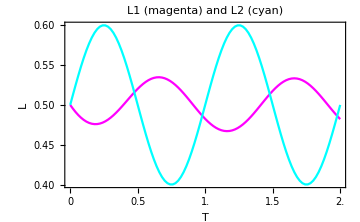

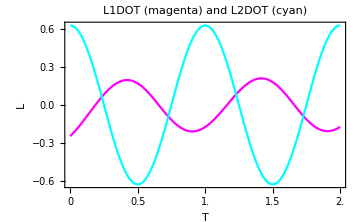

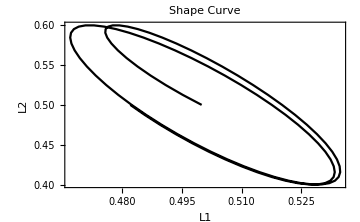

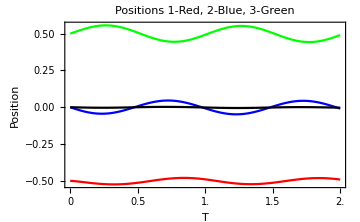

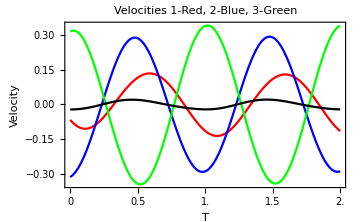

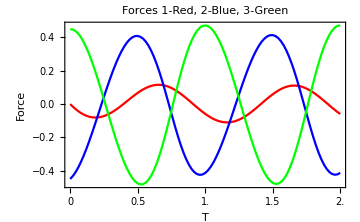

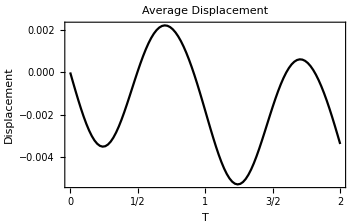

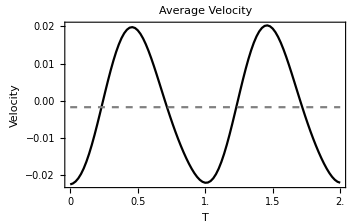

-0.00169198

```mathematica
Tmin = 0;
Tmax = 2;
Tdiff = (Tmax - Tmin)/100;

L1Data = Table[L1starred, {T, Tmin, Tmax, Tdiff}];
L2Data = Table[L2star, {T, Tmin, Tmax, Tdiff}];
L1DOTData = Table[L1DOTstarred, {T, Tmin, Tmax, Tdiff}];
L2DOTData = Table[L2DOTstar, {T, Tmin, Tmax, Tdiff}];

V1Data = Table[V1starred, {T, Tmin, Tmax, Tdiff}];
V2Data = Table[V2starred, {T, Tmin, Tmax, Tdiff}];
V3Data = Table[V3starred, {T, Tmin, Tmax, Tdiff}];
VSData = Table[VSstarred, {T, Tmin, Tmax, Tdiff}];
F1Data = Table[F1starred, {T, Tmin, Tmax, Tdiff}];
F2Data = Table[F2starred, {T, Tmin, Tmax, Tdiff}];
F3Data = Table[F3starred, {T, Tmin, Tmax, Tdiff}];

D1Data = Table[ NIntegrate[V1starred, {T, Tmin, τ}], {τ, Tmin, Tmax, Tdiff}];
D2Data = Table[ NIntegrate[V2starred, {T, Tmin, τ}], {τ, Tmin, Tmax, Tdiff}];
D3Data = Table[ NIntegrate[V3starred, {T, Tmin, τ}], {τ, Tmin, Tmax, Tdiff}];
DSData = Table[ NIntegrate[VSstarred, {T, Tmin, τ}], {τ, Tmin, Tmax, Tdiff}];

AvgV = 1/(Tmax - Tmin)NIntegrate[VSstarred, {T, Tmin, Tmax}];

P1Data = - L1Data[[1]] + D1Data;
P2Data = 0 + D2Data;
P3Data = + L2Data[[1]] + D3Data;

Show[
ListLinePlot[L1Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Magenta}],
ListLinePlot[L2Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Cyan}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["L1 (magenta) and L2 (cyan)", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "L", Black, Bold]}
]
Show[
ListLinePlot[L1DOTData,DataRange -> {Tmin, Tmax},PlotStyle-> {Magenta}],
ListLinePlot[L2DOTData,DataRange -> {Tmin, Tmax},PlotStyle-> {Cyan}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["L1DOT (magenta) and L2DOT (cyan)", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "L", Black, Bold]}
]
Show[
ListLinePlot[Transpose[{L1Data, L2Data}], PlotStyle-> Black],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
ImageSize-> Medium,
PlotLabel -> Style["Shape Curve", Black, Bold, Italic],
FrameLabel -> {Style["L1", Black, Bold],Style[ "L2", Black, Bold]}
]
Show[
ListLinePlot[P1Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Red}],
ListLinePlot[P2Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Blue}],
ListLinePlot[P3Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Green}],
ListLinePlot[DSData,DataRange -> {Tmin, Tmax},PlotStyle-> {Black}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Positions 1-Red, 2-Blue, 3-Green", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Position", Black, Bold]}
]
Show[
ListLinePlot[V1Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Red}],
ListLinePlot[V2Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Blue}],
ListLinePlot[V3Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Green}],
ListLinePlot[VSData,DataRange -> {Tmin, Tmax},PlotStyle-> {Black}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Velocities 1-Red, 2-Blue, 3-Green", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Velocity", Black, Bold]}
]
Show[
ListLinePlot[F1Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Red}],
ListLinePlot[F2Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Blue}],
ListLinePlot[F3Data,DataRange -> {Tmin, Tmax},PlotStyle-> {Green}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Forces 1-Red, 2-Blue, 3-Green", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Force", Black, Bold]}
]
Show[
ListLinePlot[DSData,DataRange -> {Tmin, Tmax},PlotStyle-> {Black}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25Tdiff, Tmin +37.5Tdiff, Tmin +50Tdiff, Tmin +62.5Tdiff, Tmin +75Tdiff, Tmin +87.5Tdiff, Tmin +100Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Average Displacement", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Displacement", Black, Bold]}
]
Show[
ListLinePlot[VSData,DataRange -> {Tmin, Tmax},PlotStyle-> {Black}],
ListLinePlot[AvgV + Table[0, {T, Tmin, Tmax, Tdiff}], DataRange->{Tmin,Tmax}, PlotStyle->{Dashed, Gray}],
PlotRange -> All,
Frame -> True,
FrameStyle -> {Black, Thick},
FrameTicks -> {{All, None}, {{Tmin + 0 Tdiff, Tmin +12.5Tdiff, Tmin +25.0Tdiff, Tmin +37.5Tdiff, Tmin +50.0Tdiff, Tmin +62.5Tdiff, Tmin +75.0Tdiff, Tmin +87.5Tdiff, Tmin +100.0Tdiff}, None}},
ImageSize-> Medium,
PlotLabel -> Style["Average Velocity", Black, Bold, Italic],
FrameLabel -> {Style["T", Black, Bold],Style[ "Velocity", Black, Bold]}
]
AvgV
```